```mathematica
(*{{509.,181.}}*)
```

```mathematica
Show[-Graphics-,ContourPlot[(x-509)^2+(y-181)^2==100^2,{x,300,700},{y,0,400},Mesh->All]]
```

-Graphics-

中心坐标(509,181),范围(603.1,167),(553.1,94.34)

```mathematica
ArcTan[(181-167)/(509-603.1)]*180/Pi
```

-8.46227

```mathematica
ArcTan[(181-94.34)/(509-553.1)]*180/Pi
```

-63.0291

```mathematica
Manipulate[
SunPosition[GeoPosition[{30.329024,120.158668}],DateObject[{2021,月,日,小时,分钟,秒}],CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"],
{月,1,12,1},{日,1,31,1},{小时,1,24,1},{分钟,1,60,1},{秒,1,60,1}](*返回值:方位角/高度 (az/alt)*)
```

```mathematica
UnitConvert[DateObject[{2021,1,1,0,0,0}]-DateObject[0],"Seconds"]
```

3818448000 s

```mathematica
DateObject[3818448000]
```

Fri 1 Jan 2021 00:00:00GMT+8.

```mathematica
Export["P:\\Users\\a1535\\Desktop\\地理实验\\高度角与方向角的数据.xlsx",
ParallelTable[
ToString@QuantityMagnitude@SunPosition[GeoPosition[{30.329024,120.158668}](*高一一班所在的经纬度*),DateObject[3818448000+天+小时](*2021,1,1,0,0,0+天+小时*),CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"](*方位角/高度 (az/alt)*),
{小时,0,23*60*60(*把小时转化成秒*),60*60(*把一小时转化成秒*)},{天,0,364*24*60*60(*把天转化成小时*),24*60*60(*把一天转化成秒*)}
]]
```

P:\Users\a1535\Desktop\地理实验\高度角与方向角的数据.xlsx

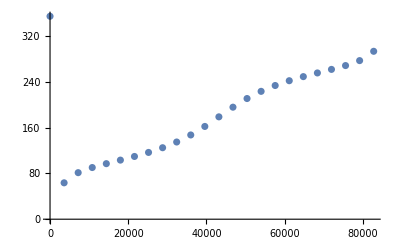

```mathematica
ListPlot[
ParallelTable[
{小时,First@QuantityMagnitude@SunPosition[GeoPosition[{30.329024,120.158668}](*高一一班所在的经纬度*),DateObject[3818448000+小时](*2021,1,1,0,0,0+天+小时*),CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"](*方位角/高度 (az/alt)*)},
{小时,0,23*60*60(*把小时转化成秒*),60*60(*把一小时转化成秒*)}
]
]
```